```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
WeightedMean[data_,weightList_]:=Total[weightList/Total@weightList*data]
FinancialChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{lists,allDates,ruleLists,listsWithMissing,mean,weighted,data,table,ts,headings},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
ruleLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,ruleLists}];
mean=Normal@Merge[listsWithMissing,Mean];
weighted=If[TrueQ[weightList==Nothing],Nothing,Normal@Merge[listsWithMissing,WeightedMean[#,weightList]&]];
data=listsWithMissing~Join~{mean,weighted};
table=Table[Select[Values@d,NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&,{d,data}];
ts=Transpose@{Keys@#,Values@#}&/@data;
headings=symbols~Join~{"Mean",If[TrueQ[weightList==Nothing],Nothing,"Weighted Mean"]};
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],TableForm[table,TableHeadings->{headings,{"Return","Standard Deviation","Return/SD"}}]}
]
```

{{AMZN,MSFT,V,BA,MA,JPM,CSCO,INTC,NFLX,ADBE},{5.50492,5.42186,4.9617,4.76633,4.55376,4.37947,3.69114,3.49097,3.36582,2.99286}}

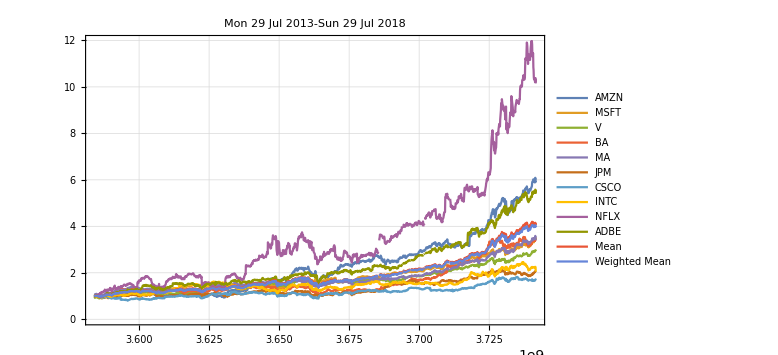
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.93685 | 1.28334 | 4.6261
MSFT | 3.41408 | 0.589292 | 5.79353
V | 2.93192 | 0.498502 | 5.88145
BA | 3.44099 | 0.685458 | 5.01999
MA | 3.39922 | 0.577349 | 5.88763
JPM | 2.0835 | 0.343896 | 6.05851
CSCO | 1.68062 | 0.238414 | 7.04914
INTC | 2.05164 | 0.325738 | 6.29842
NFLX | 10.1505 | 2.38485 | 4.25625
ADBE | 5.40195 | 1.11533 | 4.84336
Mean | 4.04913 | 0.789282 | 5.13014
Weighted Mean | 3.95193 | 0.762617 | 5.18207

```mathematica
json=Import["https://www.ishares.com/us/products/251614/ishares-msci-usa-momentum-factor-etf/1467271812596.ajax?tab=top&fileType=json","String"]//ImportString[StringDrop[#,3],"JSON"]&;
{symbols,weights}=Table[First@i->Last@Last@i[[6]],{i,Last@First@json}]//{Keys@#,Values@#}&
start=DatePlus[Today,-Quantity[5, "Years"]];
end=Today;
chart=FinancialChart[symbols,start,end,weights]
Export[FileNameJoin[{NotebookDirectory[],"chart.svg"}],chart];
```

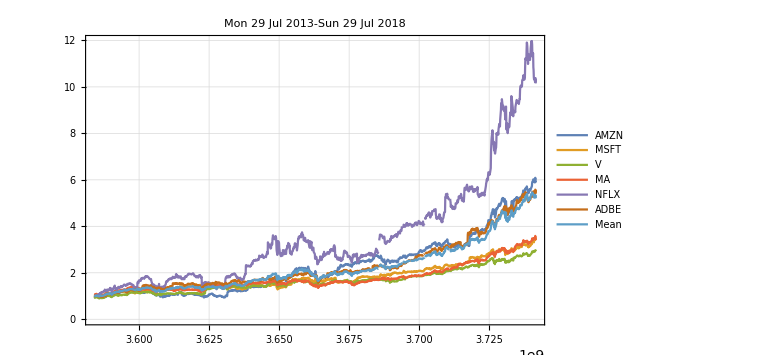
-Graphics-
 | Return | Standard Deviation | Return/SD
AMZN | 5.93685 | 1.28334 | 4.6261
MSFT | 3.41408 | 0.589292 | 5.79353
V | 2.93192 | 0.498502 | 5.88145
MA | 3.39922 | 0.577349 | 5.88763
NFLX | 10.1505 | 2.38485 | 4.25625
ADBE | 5.40195 | 1.11533 | 4.84336
Mean | 5.20575 | 1.06404 | 4.89243

```mathematica
(*weights={5.5,5.42,4.96,4.77,4.55,4.38,3.69,3.49,3.37,2.99};
symbols={"AMZN","MSFT","V","BA","MA","JPM","CSCO","INTC","NFLX","ADBE"};*)
symbols2={"AMZN","MSFT","V","MA","NFLX","ADBE"};
FinancialChart[symbols2,start,end]
```

```mathematica
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
TableForm@{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"Return","SD","Return/SD"},Automatic}]&}
]
```

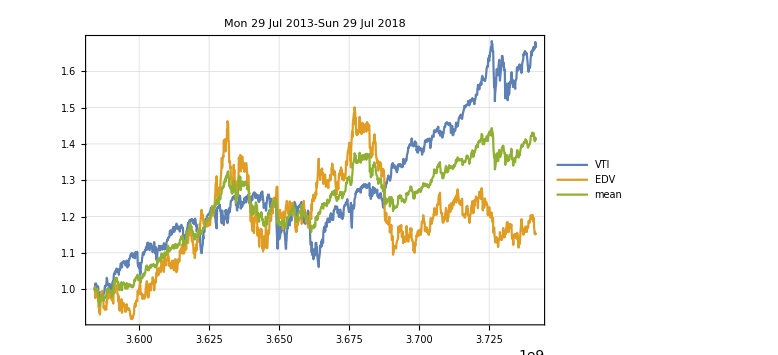
-Graphics-
Return | 1.40959
SD | 0.119416
Return/SD | 11.804

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
```